```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\LPA\runningpoint\beta\LPA_Tscaling_mub703\buffer

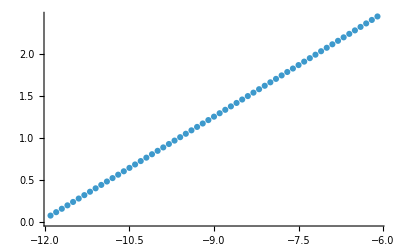

```mathematica
fpi=Flatten[Import["./fpi.dat"]];
T=Flatten[Import["./TMeV.dat"]];
cl=Flatten[Import["./TMeV.dat"]];
t=(cl-cl[[1]])/cl[[1]];
csdata=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
a1=Table[FindFit[csdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[cl]-2}];
b1600=Table[FindFit[csdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[cl]-2}];
Show[ListPlot[{csdata},PlotRange->All]]
```

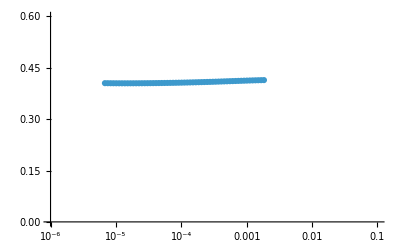

```mathematica
ListPlot[Transpose[{-t[[2;;-3]],b1600}],PlotRange->{{10^-6,10^-1},{0.,0.6}},ScalingFunctions->{"Log"}]
```